```mathematica
g2[τ_,τ0_,g20_]=1-Exp[-Abs[τ]/τ0]+(1-g20)Exp[-Abs[τ]/τ0];
gaussian[τ_,σ_]=1/(σ √(2π))Exp[-1/2(τ/σ)^2];
gaussianNotNorm[τ_,σ_]=Exp[-1/2(τ/σ)^2];
```

```mathematica
Manipulate[Plot[g2[τ,τ0,g20],{τ,-5,5},PlotRange->{{-5,5},{0,2}}],{τ0,1,5},{g20,0,2}]
```

```mathematica
Manipulate[Plot[gaussian[τ,σ],{τ,-5,5},PlotRange->{{-5,5},{0,2}}],{σ,1,5}]
```

```mathematica
Convolve[gaussian[τ,0.01],g2[τ,1,0.01],τ,ω]
```

39.8942 (0.0250663-0.99 (0.0125338 ⅇ^(-1. ω) Erfc[0.00707107-70.7107 ω]+0.0125338 ⅇ^(1. ω) Erfc[0.00707107+70.7107 ω]))

```mathematica
(*USE this one!*)g2Convolved[ω_,τ0_,g20_,σ_]=Convolve[gaussian[τ,σ],g2[τ,τ0,g20],τ,ω]
```

((√(2 π))/(√(1/σ^2))+(ⅇ^(σ^2/(2 τ0^2)-ω/τ0) (1-g20) √(π/2) (-1-ⅇ^((2 ω)/τ0)+√(1/σ^2) σ Erf[(σ^2-τ0 ω)/(√2 σ τ0)]+ⅇ^((2 ω)/τ0) √(1/σ^2) σ Erf[(σ^2+τ0 ω)/(√2 σ τ0)]))/(√(1/σ^2)))/(√(2 π) σ)

```mathematica
FullSimplify[g2Convolved[ω,τ0,g20,σ],Assumptions->{σ∈Reals,σ>0}]
```

1+1/2 ⅇ^((σ^2-2 τ0 ω)/(2 τ0^2)) (-1+g20) (Erfc[(σ^2-τ0 ω)/(√2 σ τ0)]+ⅇ^((2 ω)/τ0) Erfc[(σ^2+τ0 ω)/(√2 σ τ0)])

```mathematica
(*Do NOT use this one!*)g2ConvolvedNotNorm[ω_,τ0_,g20_,σ_]=Convolve[gaussianNotNorm[τ,σ],g2[τ,τ0,g20],τ,ω]
```

(√(2 π))/(√(1/σ^2))+(ⅇ^(σ^2/(2 τ0^2)-ω/τ0) (1-g20) √(π/2) (-1-ⅇ^((2 ω)/τ0)+√(1/σ^2) σ Erf[(σ^2-τ0 ω)/(√2 σ τ0)]+ⅇ^((2 ω)/τ0) √(1/σ^2) σ Erf[(σ^2+τ0 ω)/(√2 σ τ0)]))/(√(1/σ^2))

```mathematica
g2Convolved[0,1,0.04,0.5]
```

0.328732

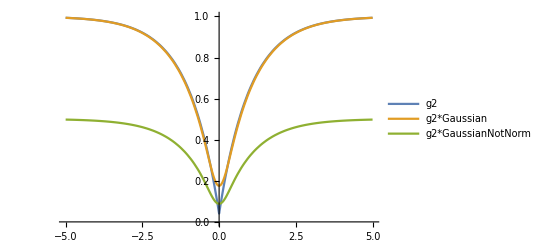

```mathematica
Plot[{g2[τ,1,0.04],g2Convolved[τ,1,0.04,0.2],g2ConvolvedNotNorm[τ,1,0.04,0.2]},{τ,-5,5},PlotLegends->{"g2","g2*Gaussian","g2*GaussianNotNorm"},PlotRange->{Automatic,{0,1}}]
```

Clearly we should used the normalized gaussian[]